# Random Walks

## Random Walk in 1 Dimension

```mathematica
randomWalk1D = Table[NestList[# + RandomChoice[{-1,1}]&,0,500],1000];
```

```mathematica
ListLinePlot[randomWalk1D]
```

-Graphics-

```mathematica
position = Map[#[[Length[#]]]& ,randomWalk1D];
```

```mathematica
meanPosition = Mean[position]
standardDeviationPosition = N[StandardDeviation[position]]
```

-84/125

22.6095

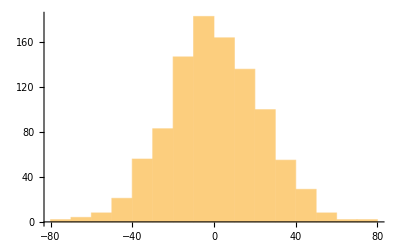

```mathematica
Histogram[position]
```

```mathematica
distances = Map[Abs[#[[Length[#]]]]& ,randomWalk1D];
```

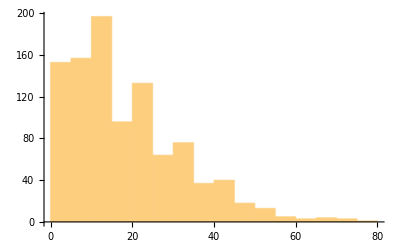

```mathematica
meanDistances = Mean[distances];
standardDeviationDistances= N[StandardDeviation[position]];
Histogram[distances]
```

## Random Walk in 2 Dimensions

```mathematica
randomWalk2D = Table[NestList[# + RandomChoice[{{1,0},{0,1},{0,-1},{-1,0}}]&,{0,0},500],1000];
```

```mathematica
ListLinePlot[randomWalk2D]
```

-Graphics-

```mathematica
position2D = Map[#[[Length[#]]]& ,randomWalk2D];
Mean2DPosition = N[Mean[position2D]]
StandardDeviation2DPosition = N[StandardDeviation[position2D]]
```

{0.281,0.595}

{15.5618,16.0301}

```mathematica
Histogram3D[position2D]
```

-Graphics3D-

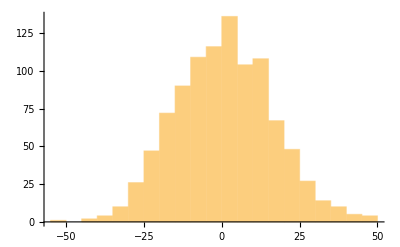
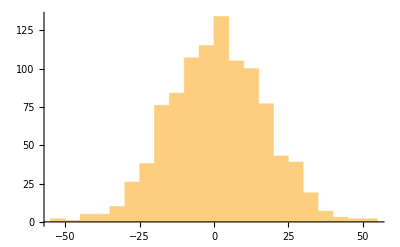

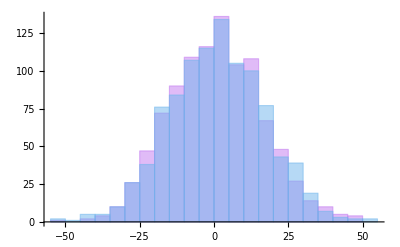

```mathematica
yposition2D = #[[2]]&/@ position2D;
xposition2D=#[[1]]&/@ position2D;
Table[Histogram[x],{x,{xposition2D,yposition2D}}]
Histogram[{xposition2D,yposition2D},ChartStyle->"Pastel"]
```

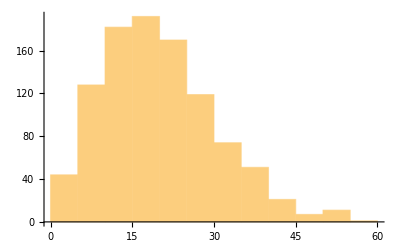

```mathematica
distance2D = Sqrt[#[[1]]^2+#[[2]]^2]&/@position2D;
Mean2DDistance = Mean[distance2D];
StandardDeviation2DDistance = StandardDeviation[distance2D];
Histogram[distance2D]
```

## Random Walk in 3 Dimensions

```mathematica
ListLinePlot3D[Table[NestList[# + RandomChoice[{{1,0,0},{0,1,0},{0,-1,0},{-1,0,0},{0,0,1},{0,0,-1}}]&,{0,0,0},100],1000]]
```

-Graphics3D-